# Mood Detection in Human Speech

Dev Chheda

Mentor: Faizon Zaman

## Abstract

We designed a system which is capable of detecting mood in human speech. Specifically, the system can be trained on a single user’s voice given samples of emotional speech labeled as being angry, happy, or sad. The system is then able to classify future audio clips of the user’s speech as having one of these three moods. The system first preprocesses audio clips to reduce noise, and allow for easier analysis of the audio data. Then, it extracts and analyzes features of the training data which are used to build a Classifier Function in the Wolfram Language. The analyzed features include amplitude, fundamental frequency, word rate, formants, and pausing in the audio clips. After the Classifier Function is constructed, it is tested on more preprocessed speech clips from the same speaker. We implemented many different methods for the Classifier Function and compared their accuracies to find the optimal Classifier. We found that Logistic Regression achieved the greatest accuracy. We also found that the Classifier is able to correctly classify the clips into the three moods to a great degree of accuracy, averaging 93%, even when the statement content did not match the mood of the voice.

## Introduction

Mood detection in human speech is the process of identifying the emotion in a given speech clip based on the audio features of the speech rather than the content of the speech. For example, angry speech might be characterized by louder, lower pitched speech, while sad speech might be characterized by softer, slower speech. In this project, we focussed on mood detection for one specific user. We did this because, given the limited time and scope of this project, it would have been much more difficult to create a general classifier for all speakers than to create a specific one for a single user. We discuss a general classifier and other expansions in Future Work.

## Initial Data Collection

We used Audacity to record audio clips in 32-bit floating point resolution, exported as WAV files. The initial training and testing clips statements were specific to each mood. That is, statements with angry content were recorded in an angry mood, statements with happy content were recorded in an happy mood, and statements with sad content were recorded in an sad mood.

### Training Data

We recorded ten training statements for each mood, and imported them into Mathematica. These data are currently available on the project GitHub repository.

Import training data for each mood from the project GitHub repository

```mathematica
angryTrainingClips =Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TrainingData/angry"<>ToString[i]<>".wav"], {i, 10}];
happyTrainingClips = Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TrainingData/happy"<>ToString[i]<>".wav"], {i, 10}];
sadTrainingClips = Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TrainingData/sad"<>ToString[i]<>".wav"], {i, 10}];
```

### Testing Data

We also recorded ten different testing clips for each mood. These data are also available on the project GitHub repository.

Import testing data for each mood from the project GitHub repository

```mathematica
angryTestingClips =  Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/Regular/a"<>ToString[i]<>".wav"], {i, 10}];
happyTestingClips =  Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/Regular/h"<>ToString[i]<>".wav"], {i, 10}];
sadTestingClips =  Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/Regular/s"<>ToString[i]<>".wav"], {i, 10}];
```

## Feature Extraction

In order to produce the most accurate Classifier, we extracted features which we thought were most useful to detecting mood. We first extracted features for one clip (specifically, the first angry training clip), and then consolidated all extraction code into a single function.

### Amplitude

First, we extracted amplitude, which represents loudness, over the duration of each clip. That is, we used  AudioLocalMeasurements to partition each clip into a given number of parts, and measured amplitude at each of these parts using the RMSAmplitude feature. We created 75 partitions for each clip.

Define the number of partitions to be created

```mathematica
partitions = 75;
```

Since AudioLocalMeasurements takes the duration of each partition as an argument, we computed the duration of each partition as the total duration of the clip (found using AudioMeasurements) divided by our defined number of partitions.

Compute the required duration of each partition

```mathematica
partitionDuration = AudioMeasurements[angryTrainingClips[[1]], "Duration"]/partitions;
```

Now, we extracted the amplitudes of the clip using AudioLocalMeasurements and the computed partition duration.

Get amplitude measurements for a clip, using the PartitionGranularity option to specify the duration of each partition

```mathematica
amplLocal = AudioLocalMeasurements[angryTrainingClips[[1]], "RMSAmplitude", PartitionGranularity->partitionDuration]
```

TimeSeries[…]

### Fundamental Frequency

Next, we extracted fundamental frequency, or pitch, in the same manner as the amplitude. We used AudioLocalMeasurents again, getting the FundamentalFrequency feature, and partitioning based on our previously computed values.

Get fundamental frequency measurements for a clip, using the PartitionGranularity option to specify the duration of each partition

```mathematica
fundFreqLocal = AudioLocalMeasurements[angryTrainingClips[[1]], "FundamentalFrequency", PartitionGranularity->partitionDuration]
```

TimeSeries[…]

However, the fundamental frequency cannot always be calculated, leaving gaps in the data at the partitions where the frequency. So, we fill in the missing data using linear interpolation (i.e. with interpolation order equal to 1) with the MissingDataMethod option.

Get fundamental frequency measurements for a clip, using the MissingDataMethod option and an Interpolation of order 1 to fill in missing data

```mathematica
fundFreqlLocalFull = AudioLocalMeasurements[angryTrainingClips[[1]], "FundamentalFrequency", PartitionGranularity->partitionDuration, MissingDataMethod->{"Interpolation", InterpolationOrder-> 1}]
```

TimeSeries[…]

### Formants

Formants are the resonating frequencies in the human vocal tract. We extracted formants in the same way as amplitude and fundamental frequency, with one minor difference. AudioLocalMeasurements returns the first five formants by default, so our feature extraction returned a time series with five dimensions for formants, rather than one dimension like for the other features.

Get formant measurements for a clip, using the PartitionGranularity option to specify the duration of each partition

```mathematica
formantsLocal = AudioLocalMeasurements[angryTrainingClips[[1]], "Formants", PartitionGranularity->partitionDuration]
```

TimeSeries[…]

### Word rate

The word rate is defined here as the number of words spoken per second. First, we found the text being spoken using the experimental SpeechRecognize function. Due to its experimental nature, we used Quiet to suppress error messages from SpeechRecognize.

Extract the text from a clip, suppressing error output.

```mathematica
speech = Quiet[SpeechRecognize[angryTrainingClips[[1]]]]
```

get out of my room

Next, we used TextWords and Length to find the number of words in the speech.

Compute the number of words in a clip

```mathematica
numWords = Length[TextWords[speech]]
```

5

Finally, we found the word rate by dividing the number of words by the total duration of the clip.

Compute the word rate of a clip

```mathematica
wordRate = numWords/AudioMeasurements[angryTrainingClips[[1]], "Duration"]
```

3.0983

### Pauses

Pausing during speech can also play an important role in mood detection. Here we quantified pausing as the ratio of all pausing time in the clip to the total duration of the clip. First, we found the pausing intervals using AudioIntervals, looking for quiet parts of the clip, using the automatic Quiet option.

Find the quiet intervals, which we take to be pausing intervals, in a clip

```mathematica
pausingIntervals = AudioIntervals[angryTrainingClips[[1]], "Quiet"]
```

{{0.,0.0348299},{0.15093,0.336689},{1.26549,1.61379}}

Since the AudioIntervals function returns a list of starting and ending points of each pausing interval, we had to compute the duration of each interval by applying Subtract to each interval.

Compute the length of each pausing interval of a clip using Subtract

```mathematica
pausingDurations = Subtract @@@ pausingIntervals
```

{-0.0348299,-0.18576,-0.348299}

Since all of the duration are negative, we mapped Abs to the list of durations.

Replace each pausing duration of a clip with its absolute value

```mathematica
pausingAbsDurations = Abs /@ pausingDurations
```

{0.0348299,0.18576,0.348299}

Next, we totaled these durations to get the total pausing time.

Compute the total pausing time of a clip

```mathematica
pausingTime = Total[pausingAbsDurations]
```

0.568889

Finally, we computed the pausing ratio by dividing the total pausing time by the total duration of the clip.

Compute the pausing ratio of a clip

```mathematica
pausingRatio = pausingTime/AudioMeasurements[angryTrainingClips[[1]], "Duration"]
```

0.352518

### Consolidating Features

After we extracted all the features, we consolidated them into a single association.

#### Normalizing Data

Since the amplitude, frequency, and formant data are TimeSeries, we had to normalize them as lists first. We did this using the Normal function.

Normalize amplitude, frequency, and formant data

```mathematica
amplLocalNormal = Normal[amplLocal];
fundFreqLocalNormal=Normal[fundFreqlLocalFull];
formantsLocalNormal = Normal[formantsLocal];
```

#### Create Association

Finally, we consolidated all of the extracted features into a single association. For amplitude, frequency, and formants, we separated the lists into individual features for each partition.

Create an association of features for a clip

```mathematica
featAssoc = <|
Table["amplitude"<>ToString[i]-> amplLocalNormal[[i]][[2]], {i, Length[amplLocalNormal]}], 
Table["frequency"<>ToString[i]-> fundFreqLocalNormal[[i]][[2]], {i, Length[fundFreqLocalNormal]}], 
Table[Table["formant"<>ToString[i]<>"-"<>ToString[j]-> formantsLocalNormal[[i]][[j]], {j, Length[formantsLocalNormal[[i]]]}], {i, Length[formantsLocalNormal]}],
"wordrate"->wordRate,
"pauses"->  pausingRatio
|>;
```

### Feature Extraction Function

After we devised a method for extracting features, we combined all feature extraction into a singular function for ease-of-use. The function takes an audio object and the number of partitions and returns an association of features.

Singular function for feature extraction of a clip

```mathematica
extractFeatures[audio_, parts_] :=  Module[{assoc, pdur, amp, freq, form}, 
pdur =AudioMeasurements[audio, "Duration"]/parts;
amp = AudioLocalMeasurements[audio,"RMSAmplitude", PartitionGranularity->pdur] // Normal;
freq = AudioLocalMeasurements[audio,"FundamentalFrequency", MissingDataMethod->{"Interpolation",InterpolationOrder->1}, PartitionGranularity->pdur] // Normal;
form =  AudioLocalMeasurements[audio, "Formants", PartitionGranularity->pdur] //Normal;
assoc= <|
Table["amplitude"<>ToString[i]-> amp[[i]][[2]], {i, Length[amp]}], 
Table["frequency"<>ToString[i]-> freq[[i]][[2]], {i, Length[freq]}], 
"wordrate"->Length[TextWords[Quiet[SpeechRecognize[audio]]]]/AudioMeasurements[audio, "Duration"],
Table[Table["formant"<>ToString[i]<>"-"<>ToString[j]-> form[[i]][[j]], {j, Length[form[[i]]]}], {i, Length[form]}],
"pauses"->  Total[Abs /@ Subtract@@@AudioIntervals[audio, "Quiet"]]/AudioMeasurements[audio, "Duration"]
|>; 
Map[Normal, assoc, {1}]
]
```

## Initial Classifier

We trained the initial classifier with the constructed feature extraction method.

### Extract Data Features

First, we had to extract the features for all of the training and testing data. We defined the number of partitions to create for each clip as 75.

Define the number of partitions for each clip’s feature extraction

```mathematica
partitions = 75;
```

#### Training Data

We extracted features from the training data using the defined function. We created a new list of associations, with each association corresponding to a single clip.

Extract features from the training data

```mathematica
angryTrainingFeats = Table[extractFeatures[angryTrainingClips[[i]], partitions], {i, 10}];
happyTrainingFeats = Table[extractFeatures[happyTrainingClips[[i]], partitions], {i, 10}];
sadTrainingFeats = Table[extractFeatures[sadTrainingClips[[i]], partitions], {i, 10}];
```

#### Testing Data

We also extracted features from the testing data using the defined function. We created a new list of associations, with each association corresponding to a single clip.

Extract features from the testing data

```mathematica
angryTestingFeats = Table[extractFeatures[angryTestingClips[[i]], partitions], {i, 10}];
happyTestingFeats = Table[extractFeatures[happyTestingClips[[i]], partitions], {i, 10}];
sadTestingFeats = Table[extractFeatures[sadTestingClips[[i]], partitions], {i, 10}];
```

### Training the Classifier

We trained a ClassifierFunction using Classify with the extracted features of the training data. We used the LogisticRegression method, as through experimentation, we found that it yielded the best accuracy.

Train a classifier using the training data

```mathematica
classifier = Classify[<|"angry"->angryTrainingFeats, "happy"->happyTrainingFeats,"sad"->sadTrainingFeats|>,Method->"LogisticRegression"]
```

ClassifierFunction[…]

### Testing the Classifier

We tested the classifier on the extracted features from the testing data.

Test the classifier on the testing data

```mathematica
classifier[angryTestingFeats]
classifier[happyTestingFeats]
classifier[sadTestingFeats]
```

{angry,angry,angry,angry,angry,angry,angry,angry,angry,angry}

{happy,happy,happy,happy,happy,happy,happy,happy,happy,happy}

{sad,happy,sad,sad,sad,sad,sad,sad,happy,happy}

## Audio Preprocessing

In order to try and improve the accuracy of the Classifier, we preprocessed the audio before extracting features. We first preprocessed a single clip (specifically, the first angry training clip), and then consolidated all audio cleaning code into a single function.

### Audio Trimming

First, we trimmed silent audio off the ends of the clip using AudioTrim.

Trim silent audio from the beginning and end of a clip

```mathematica
trimmedAudio = AudioTrim[angryTrainingClips[[1]]]
```

### Audio Filtering

Then, we filtered the audio using HighpassFilter with a cutoff frequency of 300 Hertz.

Filter audio clip using a highpass filter

```mathematica
filteredAudio = HighpassFilter[trimmedAudio,Quantity[300, "Hertz"]]
```

### Audio Downsampling

Next, we downsampled the audio to a sample rate of 16000 samples per second using AudioResample. Note that the original sample rate was 44100 samples per second.

Downsample the audio to 16000 samples per second

```mathematica
resampledAudio = AudioResample[filteredAudio, 16000]
```

### Audio Cleaning Function

Then, we consolidated the audio preprocessing into a single audio cleaning function.

Define a function which cleans audio

```mathematica
cleanAudio[audio_]:= Module[{trimmed, filtered, resampled},
trimmed=AudioTrim[audio];
filtered = HighpassFilter[trimmed, Quantity[300, "Hertz"]];
(*resampled = AudioResample[filtered, 16000]*)filtered
]
```

### Clean Feature Extraction Function

We updated the feature extraction function to clean audio before extracting features.

Define an updated version of the feature extractor to include audio cleaning

```mathematica
extractCleanFeatures[audio_, parts_] :=  Module[{cleaned, assoc, pdur, amp, freq, form}, 
cleaned = cleanAudio[audio];
pdur =AudioMeasurements[cleaned, "Duration"]/parts;
amp = AudioLocalMeasurements[cleaned,"RMSAmplitude", PartitionGranularity->pdur] // Normal;
freq = AudioLocalMeasurements[cleaned,"FundamentalFrequency", MissingDataMethod->{"Interpolation",InterpolationOrder->1}, PartitionGranularity->pdur] // Normal;
form =  AudioLocalMeasurements[cleaned, "Formants", PartitionGranularity->pdur] //Normal;
assoc= <|
Table["amplitude"<>ToString[i]-> amp[[i]][[2]], {i, Length[amp]}], 
Table["frequency"<>ToString[i]-> freq[[i]][[2]], {i, Length[freq]}], 
"wordrate"->Length[TextWords[Quiet[SpeechRecognize[cleaned]]]]/AudioMeasurements[cleaned, "Duration"],
Table[Table["formant"<>ToString[i]<>"-"<>ToString[j]-> form[[i]][[j]], {j, Length[form[[i]]]}], {i, Length[form]}],
"pauses"->  Total[Abs /@ Subtract@@@AudioIntervals[cleaned, "Quiet"]]/AudioMeasurements[cleaned, "Duration"]
|>; 
Map[Normal, assoc, {1}]
]
```

## Clean Classifier

### Extracting Clean Data Features

First, we had to re-extract the features for all of the training and testing data using the new clean feature extractor.

#### Training Data

We extracted features from the training data using the newly defined function.

Re-extract features from the training data

```mathematica
angryCleanTrainingFeats = Table[extractCleanFeatures[angryTrainingClips[[i]], partitions], {i, 10}];
happyCleanTrainingFeats = Table[extractCleanFeatures[happyTrainingClips[[i]], partitions], {i, 10}];
sadCleanTrainingFeats = Table[extractCleanFeatures[sadTrainingClips[[i]], partitions], {i, 10}];
```

#### Testing Data

We also extracted features from the testing data using the newly defined function.

Re-extract features from the testing data

```mathematica
angryCleanTestingFeats = Table[extractCleanFeatures[angryTestingClips[[i]], partitions], {i, 10}];
happyCleanTestingFeats = Table[extractCleanFeatures[happyTestingClips[[i]], partitions], {i, 10}];
sadCleanTestingFeats = Table[extractCleanFeatures[sadTestingClips[[i]], partitions], {i, 10}];
```

### Training the Clean Classifier

We trained a ClassifierFunction with the extracted clean features of the training data.

Train a new clean classifier using the clean training data

```mathematica
cleanClassifier = Classify[<|"angry"->angryCleanTrainingFeats,"happy"->happyCleanTrainingFeats,"sad"->sadCleanTrainingFeats|>,Method->"LogisticRegression"]
```

ClassifierFunction[…]

### Testing the Clean Classifier

We tested the clean classifier on the extracted clean features from the testing data.

Test the clean classifier on the testing data

```mathematica
cleanClassifier[angryCleanTestingFeats]
cleanClassifier[happyCleanTestingFeats]
cleanClassifier[sadCleanTestingFeats]
```

{angry,angry,angry,angry,angry,angry,angry,angry,angry,angry}

{happy,happy,sad,happy,happy,happy,angry,happy,happy,happy}

{sad,happy,sad,sad,sad,sad,sad,sad,sad,sad}

## Neutral Statements Data

Now, we recorded neutral statements in each of the three moods. That is, we recorded ten statements whose content was emotionally neutral, but with a vocal mood of angry, happy, and sad. So we had 30 new data clips to test the Classifier with. We did this to test if the classifier was simply using the content of the speech to classify the mood or if it was really looking at the voice features.

### Neutral Statements Data Collection

We recorded 30 clips (using ten neutral statements, each recorded in all three moods) as Neutral Statements Test Data. This data was also recorded using Audacity as discussed in Initial Data Collection. We imported this data into Mathematica. These data are currently available on the project GitHub repository.

Import neutral statements testing data for each mood from the project GitHub repository

```mathematica
angryNeutralTestingClips = Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/NeutralStatements/a"<>ToString[i]<>".wav"], {i, 10}];
happyNeutralTestingClips =  Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/NeutralStatements/h"<>ToString[i]<>".wav"], {i, 10}];
sadNeutralTestingClips =  Table[Import["https://github.com/vedadehhc/MoodDetector/raw/master/AudioData/TestingData/NeutralStatements/s"<>ToString[i]<>".wav"], {i, 10}];
```

### Extract Neutral Statements Data Features

Then, we extracted the features from the neutral statements data using the previously defined function.

Extract features from the neutral statements testing data

```mathematica
angryNeutralTestingFeats = Table[extractCleanFeatures[angryNeutralTestingClips[[i]], partitions], {i, 10}];
happyNeutralTestingFeats = Table[extractCleanFeatures[happyNeutralTestingClips[[i]], partitions], {i, 10}];
sadNeutralTestingFeats = Table[extractCleanFeatures[sadNeutralTestingClips[[i]], partitions], {i, 10}];
```

### Testing the Classifier on Neutral Statements Data

Finally, we tested the classifier on the neutral statements data features.

```mathematica
cleanClassifier[angryNeutralTestingFeats]
cleanClassifier[happyNeutralTestingFeats]
cleanClassifier[sadNeutralTestingFeats]
```

{angry,angry,angry,angry,angry,angry,angry,angry,angry,angry}

{happy,angry,happy,happy,happy,happy,happy,happy,happy,happy}

{sad,sad,sad,sad,sad,sad,sad,sad,sad,sad}

## Results and Conclusions

We recorded ten clips in each mood to be used as training data, and ten different clips in each mood to be used as testing data. Many different classifiers were trained using the in-built methods for Classifier Functions in the Wolfram Language. We found that the classifiers with the best accuracies on the testing data were the Logistic Regression and Nearest Neighbors classifiers at 77% accuracy and 73% accuracy respectively. We then implemented an audio cleaning function, which boosted the accuracies of the Logistic Regression and Nearest Neighbors classifiers to 90% accuracy and 80% accuracy respectively. Through the use of feature space plots we found that there are extreme differences between the angry and sad moods (such that they are never confused for each other), while the happy mood lies between angry and sad, leading to some confusion for the Classifier. We then tested the Classifier on clips of the same statement in different moods. That is, we recorded emotionally neutral statements in each of the moods to see if the content of the speech impacted the Classifier Function in any way. We found that the Logistic Regression Classifier Function was not impacted by the content of the speech, as it achieved 97% accuracy on the neutral statements testing data. Overall, the Classifier was able to identify mood to a reasonable degree of accuracy, even when the same statements were spoken in different moods. The results are displayed in confusion matrix plots below and in a feature space plot of all 90 data clips.

Generate confusion matrix plots for the regular testing data, the neutral statements testing data, and all testing data

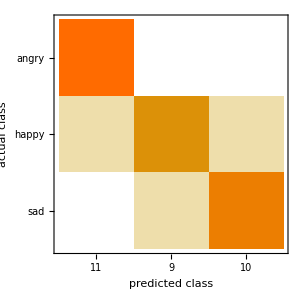
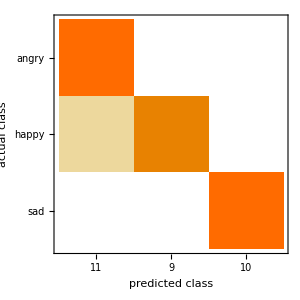
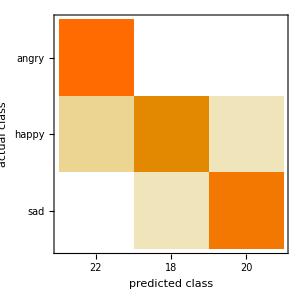
-Graphics-    Regular Test Data-Graphics-     Neutral Statements Test Data-Graphics-    All Test Data

```mathematica
cmpAngry = Table[i-> "angry", {i, angryCleanTestingFeats}];
cmpHappy = Table[i-> "happy", {i, happyCleanTestingFeats}];
cmpSad = Table[i-> "sad", {i, sadCleanTestingFeats}];
cmpNAngry = Table[i-> "angry", {i, angryNeutralTestingFeats}];
cmpNHappy = Table[i-> "happy", {i, happyNeutralTestingFeats}];
cmpNSad = Table[i-> "sad", {i, sadNeutralTestingFeats}];
Row[{Labeled[ClassifierMeasurements[cleanClassifier, Flatten@{cmpAngry, cmpHappy, cmpSad}, "ConfusionMatrixPlot"], Style["    Regular Test Data", 20], Top], Labeled[ClassifierMeasurements[cleanClassifier, Flatten@{cmpNAngry, cmpNHappy, cmpNSad}, "ConfusionMatrixPlot"],Style["     Neutral Statements Test Data", 20], Top], Labeled[ClassifierMeasurements[cleanClassifier, Flatten@{cmpAngry, cmpHappy, cmpSad,cmpNAngry, cmpNHappy, cmpNSad}, "ConfusionMatrixPlot"],Style["    All Test Data", 20], Top]}]
```

Feature space plot for all 90 data clips

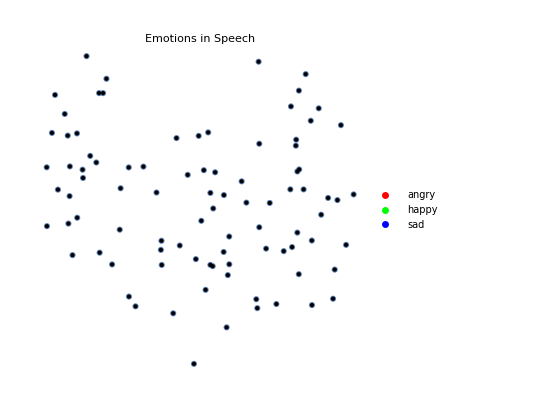

## Future Work

In the future, we hope to improve the accuracy of the Classifier by providing additional training data, and to test it further with additional testing data. We also hope to expand the range of moods the the Classifier handles, including moods such as fear, calmness, and excitement. This, of course, would require the aforementioned additional data, and perhaps, more complex structures for the Classifier Function. In the future we may also want to experiment with multiple speakers, and determine whether classifiers for one speaker’s moods can be used to determine those of another speaker.